```mathematica
λ=142.5*I;
soluciones=Solve[-2 (λ+λ^3)+(3+9 λ^2) z-12 λ z^2+(3+λ^2) z^3==0,z]
z1=z/.soluciones[[1]]
z2=z/.soluciones[[2]]
z3=z/.soluciones[[3]]
```

{{z→-5.30555+3.49104 ⅈ},{z→0.-7.0663 ⅈ},{z→5.30555+3.49104 ⅈ}}

-5.30555+3.49104 ⅈ

0.-7.0663 ⅈ

5.30555+3.49104 ⅈ

```mathematica
p[z_]:=(z^2-1)(z-λ);lp[z_]=p[z]p''[z]/p'[z]/p'[z];sp[z_]=z-1/(1-lp[z])p[z]/p'[z];
iterSch= Compile[{{z,_Complex}},sp[z]];
r1=1;r2=-1;r3=λ;
Clear[rootPosition]
rootPosition[z_]:= 
Which[Abs[z - r1] <  10.0^(-6), 3,
	       Abs[z - r2] <  10.0^(-6), 2,
	       Abs[z -r3] <  10.0^(-6), 1,
	       True, 0]
Clear[iterColorAlgorithm,colorLevel,fractalColor,plotColorFractal]
iterColorAlgorithm[iterMethod_,x_,y_,lim_] :=
Block[{z,ct,r}, z = x + y I; ct = 0;r = rootPosition[z];
While[(r==0) && (ct < lim),++ct;
z = iterMethod[z];r = rootPosition[z]
];
If[Head[r]==Which,r =0]; (* "Which" unevaluated *)
Return[N[r+ct/(lim+0.001)]]
]
colorLevelWS= Compile[{{p,_Real}},0.4*FractionalPart[p]];
fractalColorWS[p_] :=
Block[{pp = colorLevelWS[p]},
Switch[IntegerPart[p],
3, CMYKColor[0.6+pp,0.,0.,2*pp],
2, CMYKColor[0.,0.6+pp,0.,2*pp],
1, CMYKColor[0.,0.,0.6+pp,2*pp],
0, CMYKColor[0.,0.,0.,1.]
]
]
ft[min_,max_,pt_,nTicks_]:=Block[{taux,j,stepTicks=(max-min)/(nTicks-1)},
taux=Table[{pt*(j-1)/(nTicks-1)+1,min+(j-1)*stepTicks},{j,1,nTicks}]
]
plotColorFractal[iterMethod_,points_]:=
Block[{$Messages = {},
stepx=(xxMax-xxMin)/points,stepy=(yyMax-yyMin)/points},
ArrayPlot[Table[iterColorAlgorithm[iterMethod,x,y,limIterations],
{y,yyMax,1.00001*yyMin,-stepy},
{x,xxMin,1.00001*xxMax,stepx}],
FrameTicks->{ft[yyMax,yyMin,points,5],ft[xxMin,xxMax,points,5]},
PlotRange->{0,4},(* Three roots *)
ColorFunctionScaling->False,
ColorFunction->fractalColorWS
]
]
```

```mathematica
numberPoints =512;
limIterations=50;
xxMin=-3.; xxMax=3; yyMin=-10; yyMax=-4;
plotColorFractal[iterSch, numberPoints]
```

-Graphics-

```mathematica
numberPoints =512;
limIterations=50;
xxMin=2; xxMax=2.375; yyMin=-7; yyMax=-6.5;
plotColorFractal[iterSch, numberPoints]
```

-Graphics-

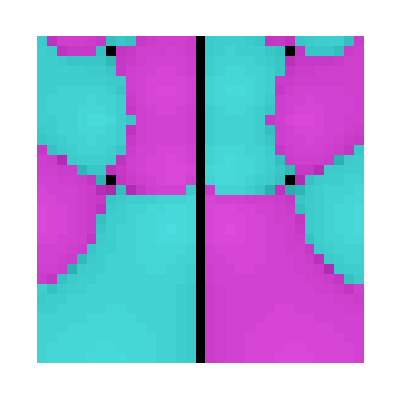

```mathematica
numberPoints =32;
limIterations=50;
xxMin=-100000; xxMax=100000; yyMin=-100000; yyMax=100000;
plotColorFractal[iterSch, numberPoints]
```

```mathematica
NestList[sp,z1,100]
```

{-5.30555+3.49104 ⅈ,-0.396626-0.223286 ⅈ,-0.762655-0.283687 ⅈ,-1.03969-0.0784115 ⅈ,-1.00191+0.00318616 ⅈ,-1.-6.04782×10^-6 ⅈ,-1.+2.01812×10^-11 ⅈ,-1.-2.51356×10^-22 ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ}

```mathematica
NestList[sp,z2,100]
```

{0.-7.0663 ⅈ,0.+0.45713 ⅈ,0.+1.14931 ⅈ,0.-7.1 ⅈ,0.+0.45714 ⅈ,0.+1.14935 ⅈ,0.-7.09825 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09842 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ}

```mathematica
NestList[sp,z3,100]
```

{5.30555+3.49104 ⅈ,0.396626-0.223286 ⅈ,0.762655-0.283687 ⅈ,1.03969-0.0784115 ⅈ,1.00191+0.00318616 ⅈ,1.-6.04782×10^-6 ⅈ,1.+2.01812×10^-11 ⅈ,1.-2.51356×10^-22 ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ}

```mathematica
NestList[sp,-17/2*I,100]
```

{-(17 ⅈ)/2,0.+0.473137 ⅈ,0.+1.21244 ⅈ,0.-5.11115 ⅈ,0.+0.502294 ⅈ,0.+1.33623 ⅈ,0.-3.36606 ⅈ,0.+0.700725 ⅈ,0.+2.73825 ⅈ,0.-0.80203 ⅈ,0.-4.52344 ⅈ,0.+0.542574 ⅈ,0.+1.52957 ⅈ,0.-2.25331 ⅈ,0.+1.13582 ⅈ,0.-7.76285 ⅈ,0.+0.46118 ⅈ,0.+1.16499 ⅈ,0.-6.46501 ⅈ,0.+0.460623 ⅈ,0.+1.16282 ⅈ,0.-6.54561 ⅈ,0.+0.459722 ⅈ,0.+1.15932 ⅈ,0.-6.68009 ⅈ,0.+0.458533 ⅈ,0.+1.15472 ⅈ,0.-6.86648 ⅈ,0.+0.457497 ⅈ,0.+1.15072 ⅈ,0.-7.03735 ⅈ,0.+0.457137 ⅈ,0.+1.14934 ⅈ,0.-7.0987 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09838 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ,0.+1.14934 ⅈ,0.-7.09841 ⅈ,0.+0.457139 ⅈ}